## 3.029 Spring 2022 Lecture 15 - 03/28/2022

## Chemical Potential Common Tangent

Last lecture, we introduced partial molar quantities, and the tangent-intercept rule

In particular we saw how the chemical potential can be obtained graphically from molar free energy plots

In this lecture, we will investigate miscibility gaps using the common-tangent construction

## Solution Models Overview

Recall the molar GIbbs free energy of mixing for an ideal solution, is given simply by the configurational entropy

```mathematica
molarGibbsEnergy["Ideal"][T_,R_:8.314][xB_]=R T ((1-xB) Log[1-xB]+xB Log[xB]);
```

Similarly for the regular solution, we introduce an enthalpic contribution due to inter-particle interactions

Where we’ve introduced

```mathematica
molarGibbsEnergy["Regular"][ω_,T_,R_:8.314][xB_]=(1-xB) xB ω+R T ((1-xB) Log[1-xB]+xB Log[xB]);
```

Finally, for a general solution model - we additionally introduce activity coefficients in the configurational entropy

This allows us to introduce asymmetric molar free energies w/ different chemical potentials of the pure compounds

```mathematica
molarGibbsEnergy["General"][γA_,γB_,ω_,T_,R_:8.314][xB_]=(1-xB) xB ω+R T ((1-xB) Log[γA(1-xB)]+xB Log[γB xB]);
```

```mathematica
Manipulate[
Plot[{
molarGibbsEnergy["Ideal"][temperature][xB],
molarGibbsEnergy["Regular"][ω,temperature][xB],
molarGibbsEnergy["General"][γA,γB,ω,temperature][xB]
},{xB,0,1},PlotStyle->Thread[{{Red,Blue,Black},Thick}],Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,PlotLegends->LineLegend[Automatic,{"Ideal Solution Model","Regular Solution Model","General Solution Model"}],FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}],
{{temperature,1},.001,1},
Delimiter,
{{ω,1},-5,5},
Delimiter,
{{γA,0.8},0.5,1.5},{{γB,1.2},0.5,1.5},
Paneled->False,SaveDefinitions->True
]
```

## Common Tangent Construction

Adding enthalpic contributions in  the regular and general solution models above introduces a competition between interactions and the configurational entropy at low temperatures, manifesting in the loss of convexity

As we’ve seen before, a loss of convexity in thermodynamic potentials suggests a phase transition

In particular, this introduces a range of compositions where the free energy of a single homogeneous solution is higher than the weighted-average of the mechanical mixture of two solutions with the same average composition

As such, the homogenous solution separates into two homogenous solutions with different compositions each to reach equilibrium

At a single temperature, these limiting compositions can be computed with the common tangent construction

Similar to L05 and P02, we will compute the common tangent construction numerically using FindRoot and the appropriate equations given below

where  are the two limiting compositions of the two-phase region on the A-rich and B-rich sides respectively

```mathematica
chemicalPotentialA["General"][γA_,γB_,ω_,T_,R_:8.314][xB_]=molarGibbsEnergy["General"][γA,γB,ω,T,R][xB]-xB molarGibbsEnergy["General"][γA,γB,ω,T,R]'[xB];
```

First, we want to check if the function indeed loses convexity

We’ll use a built-in function we introduced in L06

```mathematica
convexQ[modelName_][params__]:=FunctionConvexity[{molarGibbsEnergy[modelName][params][xB],1>xB>0},xB]===1
```

```mathematica
convexQ["General"][0.8,1.1,-1,0.25]
convexQ["General"][0.8,1.1,5,0.25]
```

True

False

We’ll use a similar lookup-table approach for initial guesses

Notice we now have a multidimensional coordinate space (γA,γB,ω,T)

In-fact, let’s also use the same mechanism to store our results

```mathematica
Clear[commonTangentConstruction,commonTangentResults]

commonTangentResults["General"]=<|{0.8,1.1,5,0.25}-><|
"compositions"->{0.15,0.85},
"function"->molarGibbsEnergy["General"][0.8,1.1,5,0.25]|>
|>;

commonTangentConstruction[modelName_][params__]:=Module[{
reversedGuesses,guessesX,sol,pw,initialGuess={0.8,1.1,5,0.25}},

If[{params}!=initialGuess&&KeyExistsQ[commonTangentResults[modelName],{params}],
Return[commonTangentResults[modelName][{params}]]];

If[convexQ[modelName][params],
AssociateTo[commonTangentResults[modelName],{params}-><|
"compositions"->{-1,2},
"function"->molarGibbsEnergy[modelName][params]|>];
Return[commonTangentResults[modelName][{params}]]];

reversedGuesses=AssociationMap[Reverse,commonTangentResults[modelName]];
guessesX=First[Nearest[reversedGuesses,{params}]]["compositions"];

sol=Quiet@FindRoot[{
chemicalPotentialA[modelName][params][x1]==chemicalPotentialA[modelName][params][x2],
molarGibbsEnergy[modelName][params]'[x1]==molarGibbsEnergy[modelName][params]'[x2]
},
{x1,guessesX[[1]]},{x2,guessesX[[2]]}];

pw=Piecewise[{{molarGibbsEnergy[modelName][params][x1]+molarGibbsEnergy[modelName][params]'[x1] (#-x1),x2>#>x1}},molarGibbsEnergy[modelName][params][#]]&/.sol;

AssociateTo[commonTangentResults[modelName],{params}-><|
"compositions"->{x1,x2}/.sol,
"function"->pw|>];

commonTangentResults[modelName][{params}]
]
```

Let’s see how this looks interactively!

```mathematica
Manipulate[
Block[{asc,pts,func},
asc=commonTangentConstruction["General"][γA,γB,ω,temperature];
{pts,func}=Values[asc];
Plot[{func[xB],molarGibbsEnergy["General"][γA,γB,ω,temperature][xB]},{xB,0,1},Filling->{1->{2}},GridLines->{pts,None},GridLinesStyle->Directive[Gray, Dashed],PlotStyle->{{Red,Thick},{Black,Thick}},Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,PlotLegends->LineLegend[Automatic,{"Common Tangent Construction","General Solution Model"}],FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}]],
{{temperature,0.25},.001,1},
Delimiter,
{{ω,5},-5,5},
Delimiter,
{{γA,0.8},0.5,1.5},{{γB,1.2},0.5,1.5},
Paneled->False
]
```

## Miscibility Gap

Note we got different limiting concentrations for each temperature

Repeating the construction over a range of temperatures, we can construct the miscibility gap of the two-phase region

i.e. concentrations for which the homogeneous solution phase-separates

we will connect these using tie-lines to illustrate the coexistence between the two phases

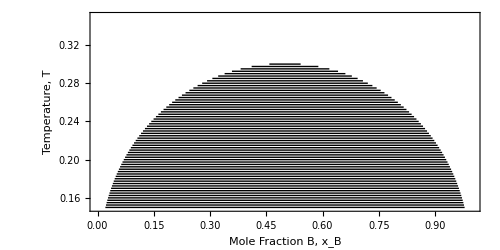

```mathematica
Do[commonTangentConstruction["General"][0.8,1.1,5,T],{T,Join[Range[0.25,0.3,0.0025],Range[0.25- 0.0025,0.15,-0.0025]]}]
tieLines=KeyValueMap[Line[Thread[{#2["compositions"],Last[#1]}]]&,KeySelect[commonTangentResults["General"],Take[#,3]=={0.8,1.1,5}&]];
Graphics[tieLines,AspectRatio->1/2,FrameLabel->{"Mole Fraction B, x_B","Temperature, T"},Frame->True,PlotRange->{{0,1},{0.15,0.35}},PlotRangeClipping->True,ImageSize->500,BaseStyle->18]
```

#### Lever Rule

The miscibility gap indicates the unstable range of compositions the two phases separate into

The composition of each phase is determined by the limits of the miscibility gap

In order to know the fraction of each phase in the two phase region, the lever rule is used

where the lever lengths are determined by the compositions as

## Convex Hull Construction

In a binary compound, there are more than two competing phases and finding all common tangent constructions between these phases using the previous technique can become cumbersome

Instead, we’ll demonstrate an equivalent technique using a computational geometry technique called the convex hull

In-fact, we’ve already seen this when we were exploring the Legendre transform using supporting hyperplanes

Let’s start by defining a binary compound with three phases given by

```mathematica
Clear[phase]
phase[name_][T_][xs_List]:=phase[name][T]/@xs

phase["A"][T_][xB_]=molarGibbsEnergy["General"][0.9,1.1,3,T][xB];
phase["B"][T_][xB_]=molarGibbsEnergy["General"][1.2,0.9,3,T][xB];
phase["C"][T_][xB_]=molarGibbsEnergy["General"][0.9,0.9,4,T][xB];
```

```mathematica
Manipulate[Plot[{
phase["A"][T][xB],
phase["B"][T][xB],
phase["C"][T][xB]
},{xB,0,1},PlotStyle->Thread[{{Red,Blue,Black},Thick}],Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,PlotLegends->LineLegend[Automatic,{"Phase A","Phase B","Phase C"}],FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}],{{T,0.275,"Temperature"},0.1,1},Paneled->False,SaveDefinitions->True]
```

Note our x Log [x] function is Indeterminate at x=0 | x =1

```mathematica
phase["A"][T][0]
```

Indeterminate

As such, we also define the following limits

```mathematica
phase["A"][T_][0]=phase["A"][T_][0.0]=Limit[phase["A"][T][x],x->0];
phase["A"][T_][1]=phase["A"][T_][1.0]=Limit[phase["A"][T][x],x->1];

phase["B"][T_][0]=phase["B"][T_][0.0]=Limit[phase["B"][T][x],x->0];
phase["B"][T_][1]=phase["B"][T_][1.0]=Limit[phase["B"][T][x],x->1];

phase["C"][T_][0]=phase["C"][T_][0.0]=Limit[phase["C"][T][x],x->0];
phase["C"][T_][1]=phase["C"][T_][1.0]=Limit[phase["C"][T][x],x->1];
```

We are interested in computing the convex-hull of the epigraph of the functions

and more specifically - the convex hull of the epigraph on the minimum of the functions

We’ll start by sampling the functions at evenly sampled concentration increments and returning the minimum values

```mathematica
minimumPoints[functionList_, numPts_] :=Thread[{Subdivide[numPts],Min/@Thread[Through[functionList[Subdivide[numPts]]]]}]
```

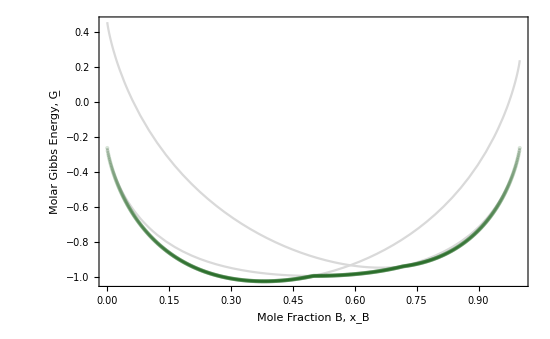

```mathematica
Plot[{
phase["A"][0.3][xB],
phase["B"][0.3][xB],
phase["C"][0.3][xB]
},{xB,0,1},PlotStyle->LightGray,Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,Epilog->{PointSize[Large],Opacity[0.15],RGBColor[0,1/3,0],Point[minimumPoints[{phase["A"][0.3],phase["B"][0.3],phase["C"][0.3]},1000]]},FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}]
```

Next, we “convexify” the function by only returning the points on the convex envelope or ‘hull’

```mathematica
getConvexHullVertices[candidatePoints_] := Module[{
maxY = Max[Last /@ candidatePoints],
amendedPoints
}, 
amendedPoints = Join[{{0., 1 + maxY}}, candidatePoints, {{1., 1 + maxY}}]; 
MeshCoordinates[ConvexHullMesh[amendedPoints]][[2;;-2]]
]
```

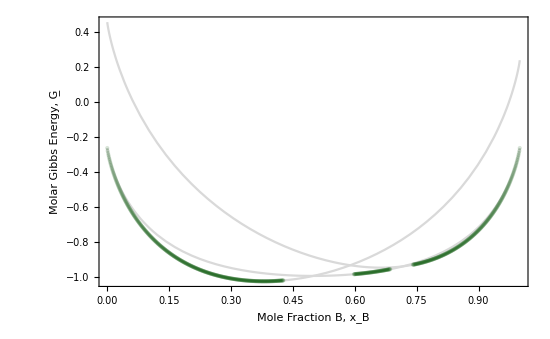

```mathematica
With[{ch=getConvexHullVertices[minimumPoints[{phase["A"][0.3],phase["B"][0.3],phase["C"][0.3]},1000]]},
Plot[{
phase["A"][0.3][xB],
phase["B"][0.3][xB],
phase["C"][0.3][xB]
},{xB,0,1},PlotStyle->LightGray,Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,Epilog->{PointSize[Large],Opacity[0.15],RGBColor[0,1/3,0],Point[ch]},FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}]]
```

As we can see, the function only returns the points on the epigraph - without connecting the common tangent points

Each “set” of points on the epigraph corresponds to a homogeneous single-phase region b/w two phases
E.g. the left-most points correspond to a single-phase region b/w Phase-A and Phase-B

We can use this to split the epigraph according to these single phase-regions

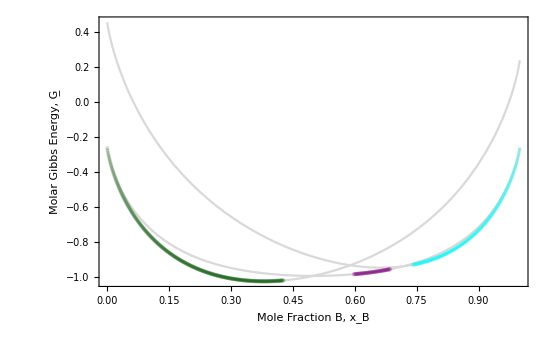

```mathematica
With[{ch=Split[getConvexHullVertices[minimumPoints[{phase["A"][0.3],phase["B"][0.3],phase["C"][0.3]},1000]],First[#2]-First[#1]<1.001/1000&]},
Plot[{
phase["A"][0.3][xB],
phase["B"][0.3][xB],
phase["C"][0.3][xB]
},{xB,0,1},PlotStyle->LightGray,Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,Epilog->{PointSize[Large],Opacity[0.15],RGBColor[0,1/3,0],Point[ch[[1]]],Purple,Point[ch[[2]]],Cyan,Point[ch[[3]]]},FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}]]
```

In-fact, we can color the single-phase region points according to their composition

and connect the various miscibility gaps with dotted lines

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
```

```mathematica
freeEnergyLineGraphicAndMiscibilityGaps[functionList_,numPts_] := 
Module[{convexHullPoints = getConvexHullVertices[minimumPoints[functionList, numPts]],
singlePhasePoints,miscibilityGaps,cf=MPLColorMap["Magma"],cols},
singlePhasePoints=Split[convexHullPoints,First[#2]-First[#1]<1.001/numPts&];
miscibilityGaps={Last[#1],First[#2]}&@@@Partition[singlePhasePoints,2,1];
cols=Map[cf[First[#]]&,singlePhasePoints,{2}];

Graphics[{Thick,MapThread[Line[#1,VertexColors->#2]&,{singlePhasePoints,cols}],Black,Dotted,Line/@miscibilityGaps}]
]
```

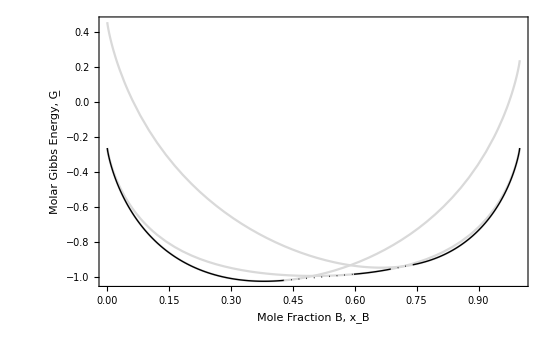

```mathematica
Show[
Plot[{
phase["A"][0.3][xB],
phase["B"][0.3][xB],
phase["C"][0.3][xB]
},{xB,0,1},PlotStyle->LightGray,Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}],
freeEnergyLineGraphicAndMiscibilityGaps[{phase["A"][0.3],phase["B"][0.3],phase["C"][0.3]},1000]]
```

Let’s see how this looks as a function of temperature

```mathematica
Manipulate[
Show[
Plot[{
phase["A"][T][xB],
phase["B"][T][xB],
phase["C"][T][xB]
},{xB,0,1},PlotStyle->LightGray,Frame->True,LabelStyle->Directive[Black,16],ImageSize->550,FrameLabel->{"Mole Fraction B, x_B","Molar Gibbs Energy, G̲"}],
freeEnergyLineGraphicAndMiscibilityGaps[{phase["A"][T],phase["B"][T],phase["C"][T]},1000]],
{{T,0.3,"Temperature"},0.1,0.75},Paneled->False]
```

## Binary Phase Diagram

Similar to the miscibility gap above, we can put all this together to plot a binary phase diagram as a function of temperature

```mathematica
backgroundGraphic[Tmin_,Tmax_]:=backgroundGraphic[Tmin,Tmax]=DensityPlot[x,{x,0,1},{y,Tmin,Tmax},ColorFunction->MPLColorMap["Magma"]][[1]]

miscibilityGaps[functionList_,temperature_,numPts_] := 
Module[{convexHullPoints = getConvexHullVertices[minimumPoints[Through[functionList[temperature]], numPts]],singlePhasePoints,miscibilityGaps,cf=MPLColorMap["Magma"],cols},
singlePhasePoints=Split[convexHullPoints,First[#2]-First[#1]<1.001/numPts&];
miscibilityGaps={Last[#1],First[#2]}&@@@Partition[singlePhasePoints,2,1];
Line/@Map[Thread[{#,temperature}]&,miscibilityGaps[[All,All,1]],{2}]
]
```

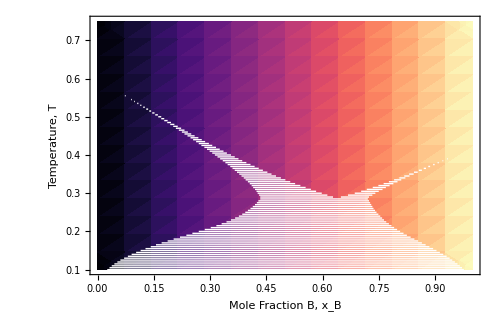

```mathematica
Graphics[{backgroundGraphic[0.1,0.75],White,miscibilityGaps[{phase["A"],phase["B"],phase["C"]},#,1000]&/@Range[0.1,0.75,0.005]},PlotRange->{{0,1},{0.1,0.75}},FrameLabel->{"Mole Fraction B, x_B","Temperature, T"},Frame->True,PlotRangeClipping->True,ImageSize->500,BaseStyle->18]
```